## Dicke Hamiltonian

```mathematica
(*Constants*)
bsize=16;ω0=1.0; ωc = 1.0; K = 4;
(*Identity matrices for TLS and QHO*)
idTSS=SparseArray[IdentityMatrix[2]];
idHO=SparseArray[IdentityMatrix[bsize]];

(*TLS initial Hamiltonian*)
H0TSS=SparseArray[Band[{1,1}]->{ω0/2,-ω0/2}];
(*QHO Hamiltonian*)
H0HO=ωc * SparseArray[Band[{1,1}]->Table[n+1/2,{n,0,bsize-1}]];
(*TLS raising and lowering operators*)
σm={{0,0},{1,0}};
σp={{0,1},{0,0}};
σx = σm + σp;

(*Annihilation operator definition*)
a=SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; 
aDaggerA=KroneckerProduct[IdentityMatrix[2^K],a†.a];
ψ0HO=KroneckerProduct[{1, 0}, SparseArray[{1->1.0},bsize]] //Flatten;

(*Function to construct the total Hamiltonian for a given j*)
Htot[j_]:=Module[{Htot,leftIds,rightIds,H0TSSi,σxi},

(*Scaled harmonic oscillator Hamiltonian,using convention with TLS on the left*)
Htot=KroneckerProduct[IdentityMatrix[2^K],H0HO];

Do[
(*Tensor product adjustment for the i-th TLS*)
leftIds=If[i>1,Table[idTSS,{i-1}],{IdentityMatrix[1]}];
rightIds=If[i<K,Table[idTSS,{K-i}],{IdentityMatrix[1]}];
(*TLS Hamiltonian for the i-th TLS*)
H0TSSi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,H0TSS],Sequence@@rightIds];
(*Adding ith TLS Hamiltonian to the total Hamiltonian*)
Htot+=KroneckerProduct[H0TSSi,idHO];
σxi=KroneckerProduct[KroneckerProduct[Sequence@@leftIds,σx],Sequence@@rightIds];
Htot+=j*(KroneckerProduct[σxi,a]+KroneckerProduct[σxi,a†]);
,{i,K}];
Htot
]
```

### Plot Attempts

Eigensystem::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigensystem.

General::stop: Further output of Eigensystem::arh will be suppressed during this calculation.

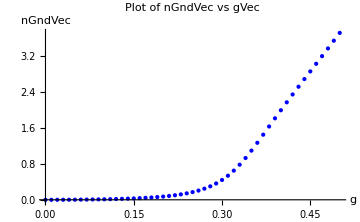

```mathematica
gVec=Table[g,{g,0.0,0.5,0.01}];

psiGndList=Table[Last[Eigensystem[constructHtot[p],-1]] //Flatten,{p,gVec}];

Do[{eigs,eigV}=Eigensystem[Htot[gVec[[n]]]];
pos=Position[eigs,Min[eigs]][[1,1]];
psiGndList[[n]]=eigV[[pos]],{n,Length[gVec]}];

(*Cavity ground state occupation probability*)
nGndVec=Table[Transpose[psi].(aDaggerA.psi),{psi,psiGndList}];
ListPlot[Transpose[{gVec,nGndVec}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"g","nGndVec"},PlotLabel->"Plot of nGndVec vs gVec", ImageSize->Medium]
```